```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[(a/y[t])Sqrt[1-y'[t]^2]+ q/y[t],y[t],t]
```

-(a+q √(1-y'[t]^2)-y'[t]^2 (a+q √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0

```mathematica
DSolve[{-(a+q √(1-y'[t]^2)-y'[t]^2 (a+q √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->1,q->3/2},y[0]==1,y'[0]==0},y[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{y[t]→3-√(4+t^2)},{y[t]→1/5 (3+√(4+25 t^2))}}

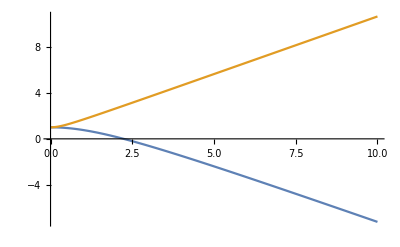

```mathematica
Plot[{3-√(4+t^2),1/5 (3+√(4+25 t^2))},{t,0,10}]
```

```mathematica
{3-√(4+t^2)/.t->3,2-√(1+t^2)/.t->3,1/2 (1+√(1+4 t^2))/.t->3,-1+√(4+t^2)/.t->3,1/3 (-1+√(16+9 t^2))/.t->3}//N
```

{-0.605551,-1.16228,3.54138,2.60555,2.94962}

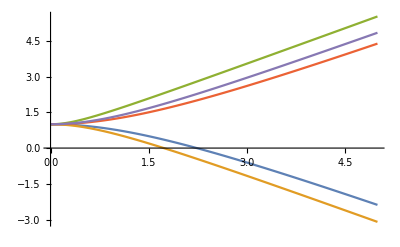

```mathematica
Plot[{3-√(4+t^2),2-√(1+t^2),1/2 (1+√(1+4 t^2)),-1+√(4+t^2),1/3 (-1+√(16+9 t^2))},{t,0,5}]
```

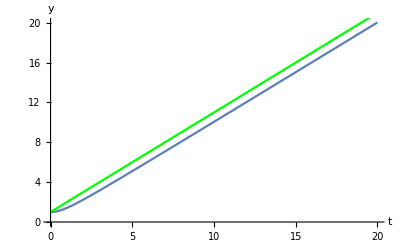

```mathematica
Block[
{y1,y2,dy,py},
y1[a1_,ys_,q1_]:=NDSolveValue[{-(a+q √(1-y'[t]^2)-y'[t]^2 (a+q √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1,q->q1},y[0]==ys,y'[0]==0},y[t],{t,0,20}];
y2[t1_,a_,ys_,q_]:=y1[a,ys,q]/.{t->t1};
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,1,0.01]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,1,300]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green]
]
];
]
```

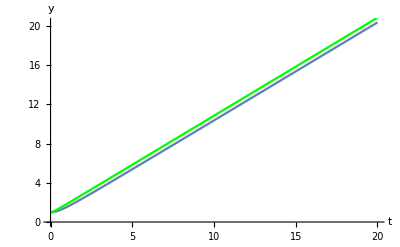

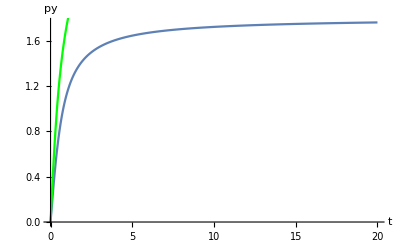

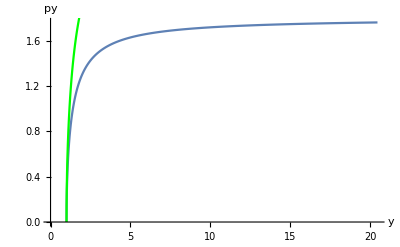

```mathematica
Block[
{y1,y2,dy,py},
y1[a1_,ys_,q1_]:=NDSolveValue[{-(a+q √(1-y'[t]^2)-y'[t]^2 (a+q √(1-y'[t]^2))-a y[t] y''[t])/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1,q->q1},y[0]==ys,y'[0]==0},y[t],{t,0,20}];
y2[t1_,a_,ys_,q_]:=y1[a,ys,q]/.{t->t1};
dy[t1_,a_,ys_,q_]:=D[y1[a,ys,q],t]/.{t->t1};
py[t1_,a_,ys_,q_]:=a/y2[t1,a,ys,q]*dy[t1,a,ys,q]/Sqrt[1-dy[t1,a,ys,q]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,1,0.5]},{i,0,20,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,1,5]},{i,0,20,0.05}],AxesLabel->{t,y},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,1,0.8]},{i,0,20,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,1,2]},{i,0,20,0.05}],AxesLabel->{t,py},PlotStyle->Green]
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,1,0.8],py[i,1,1,0.8]},{i,0,20,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,1,2],py[i,1,1,2]},{i,0,20,0.05}],AxesLabel->{y,py},PlotStyle->Green]
]
];
]
```

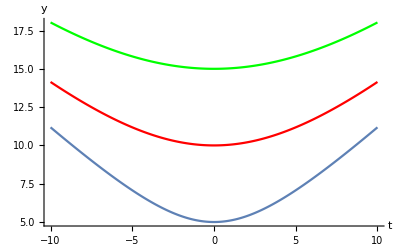

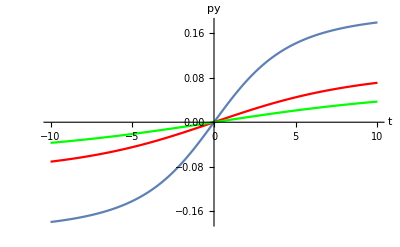

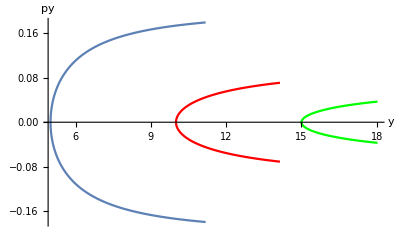

```mathematica
Block[
{y1,y2,dy,py},
y1[a1_,ys_]:=NDSolveValue[{(a (-1+y'[t]^2+y[t] y''[t]))/(y[t]^2 (1-y'[t]^2)^(3/2))==0/.{a->a1},y[0]==ys,y'[0]==0},y[t],{t,-10,10}];
y2[t1_,a_,ys_]:=y1[a,ys]/.{t->t1};
dy[t1_,a_,ys_]:=D[y1[a,ys],t]/.{t->t1};
py[t1_,a_,ys_]:=a/y2[t1,a,ys]*dy[t1,a,ys]/Sqrt[1-dy[t1,a,ys]^2];
Print[
Show[
ListLinePlot[Table[{i,y2[i,1,05]},{i,-10,10,0.05}],AxesLabel->{t,y}],
ListLinePlot[Table[{i,y2[i,1,10]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Red],
ListLinePlot[Table[{i,y2[i,1,15]},{i,-10,10,0.05}],AxesLabel->{t,y},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{i,py[i,1,05]},{i,-10,10,0.05}],AxesLabel->{t,py}],
ListLinePlot[Table[{i,py[i,1,10]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Red],
ListLinePlot[Table[{i,py[i,1,15]},{i,-10,10,0.05}],AxesLabel->{t,py},PlotStyle->Green],
PlotRange->All
]
];
Print[
Show[
ListLinePlot[Table[{y2[i,1,05],py[i,1,05]},{i,-10,10,0.05}],AxesLabel->{y,py}],
ListLinePlot[Table[{y2[i,1,10],py[i,1,10]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Red],
ListLinePlot[Table[{y2[i,1,15],py[i,1,15]},{i,-10,10,0.05}],AxesLabel->{y,py},PlotStyle->Green],
PlotRange->All
]
];
]
```